Download the QuEST Mathematica package

```mathematica
Import["http://quest.qtechtheory.org/QuEST.m"]
```

Connect to the remote Igor server (which must be running)

```mathematica
env = CreateRemoteQuESTEnv[];
```

Create two 25-qubit registers, which are stored on Igor

```mathematica
ψ = CreateQureg[25];
ϕ = CreateQureg[25];
```

```mathematica
InitPlusState[ψ];
InitPlusState[ϕ];
```

An example computation done lightning fast using Igor’s Quadro P6000

```mathematica
u[θ_] := Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]] Subscript[Ry, 3][θ] Subscript[H, 2] Subscript[X, 3] Subscript[T, 3] Subscript[C, 0][Subscript[X, 1]]
```

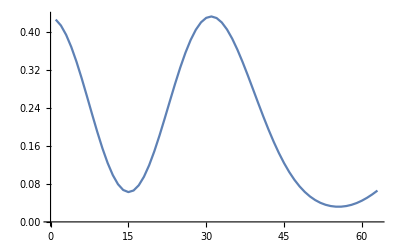

```mathematica
ListLinePlot @  Table[
	CalcFidelity[ψ, ApplyCircuit[u[θ],ψ,ϕ]],
	{θ, 0, 2π, .1}
]
```

```mathematica
DestroyAllQuregs[];
```

Disconnect from Igor

```mathematica
DestroyQuESTEnv[env];
```